```mathematica
Avoided Crossing Calculations
```

Avoided Calculations Crossing

1.) Equations of motion of a two coupled oscillator system

```mathematica
m1*x1[t]''+k1*x1[t]+k*(x1[t]-x2[t])==0;
m2*x2[t]''+k2*x2[t]-k*(x1[t]-x2[t])==0;
```

2.) Make ansatz of solution (xi[t]=Ai*Exp[-I*w(+-)*t] and plug into equations above

```mathematica
-m1*w^2*A1+k1*A1+k*(A1+A2)==0;
-m2*w^2*A2*k2*A2-k*(A1-A2)==0;
```

3.) Write equations in matrix form such that when M is multiplied by {A1,A2}, the product is zero

```mathematica
MatrixForm[M={{-m1*w^2+k1+k,-k},{-k,-m2*w^2+k2+k}}]
```

(1-w^2 | 0
0 | 1+dk-w^2)

4.) In order for this to be solvable, the determinant of M must be zero

```mathematica
Solve[Det[M]==0,{w}]
```

{{w→-1},{w→1},{w→-√(1+dk)},{w→√(1+dk)}}

5.) Only positive values of w make sense here, so them we get w+ (defined below as wp) and w- (defined below as wm). These are simplified below using the definitions w1 = Sqrt[(k1+k)/m1] and w2 = Sqrt[(k2+k)/m2].

```mathematica
k2=k1+dk;
```

```mathematica
wp[dk_]:=(√(k/m1+k1/m1+k/m2+k2/m2-(√(-4 (k k1+k k2+k1 k2) m1 m2+(-k m1-k2 m1-k m2-k1 m2)^2))/(m1 m2)))/(√2)
```

```mathematica
wm[dk_]:=(√(k/m1+k1/m1+k/m2+k2/m2+(√(-4 (k k1+k k2+k1 k2) m1 m2+(-k m1-k2 m1-k m2-k1 m2)^2))/(m1 m2)))/(√2)
```

6.) Graph solutions to show crossing

```mathematica
k1 =1;
k2=k1+dk;
m1=1;
m2=1;
k=0.1;
```

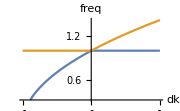

```mathematica
Plot[{wp[dk],wm[dk]},{dk,-1,1}, AxesLabel-> {"dk" ,"freq"}]
```

```mathematica
"
```

```mathematica
k1 =1;
k2=k1+dk;
m1=1;
m2=1;
k=0;
```

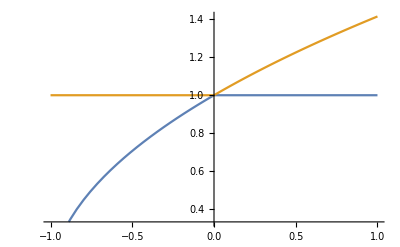

```mathematica
Plot[{wp[dk],wm[dk]},{dk,-1,1}]
```